## Outline of the solution

Hamiltonian:

H = -^2/(2m)∂^2/(∂x^2)+V0 (Cos[kx])^2

If V0 is in units of Er, where

Er =(^2 k^2)/(2m)

then the Hamiltonian is

H = -1/k^2∂^2/(∂x^2)+V0 (Cos[kx])^2

Bloch states: (k=2π/λ=π/d)

Ψ(q,n,x)= ∑_(m=-N)^N c(q,n,m)e^(iqx +im2kx)

Applying the Hamiltonian on the Bloch states:

V0(Cos[kx])^2=V0/4(2+e^i2kx+e^(-2ikx))
HΨ = ∑_(m=-N)^N (^2/(2m)(q+2mk)^2+V0/4(2+e^i2kx+e^(-2ikx)))c(q,n,m) e^(iqx +im2kx)  
HΨ=∑_(m=-N)^N ((^2/(2m)(q+2mk)^2+V0/2)c(q,n,m)+V0/4 c(q,n,m-1)+V0/4 c(q,n,m+1)) e^(iqx +im2kx)  
EΨ = ∑_(m=-N)^N E c(q,n,m) e^(iqx +im2kx)

This leads to the system of equations given by

(^2/(2m)(q+2mk)^2+V0/2)c(q,n,m)+V0/4 c(q,n,m-1)+V0/4 c(q,n,m+1)=E c(q,n,m)

For the Hamiltonian expressed in units of the recoil energy this is

((q/k+2m)^2+V0/2)c(q,n,m)+V0/4 c(q,n,m-1)+V0/4 c(q,n,m+1)=E c(q,n,m)

And if we further express the quasimomentum in units of k (k is momentum of lattice photon)

((q+2m)^2+V0/2)c(q,n,m)+V0/4 c(q,n,m-1)+V0/4 c(q,n,m+1)=E c(q,n,m)

This is a linear system of equations for the coefficients c(q,n,m).  It is an eigenvalue problem, the solution is obtained below.

The derivation of the equations for the eigenvalue problem follows the one done in the review paper by Morsch and Oberthaler:   Dynamics of Bose-Einstein condensates in optical lattices.

## Eigenvalues and eigenfunctions

```mathematica
Clear[H];H[NPoints_,q_,V0_] := SparseArray[{{i_,i_}:>((q+2(i-1-NPoints))^2+V0/2), {i_,j_} /; i-j == 1 :>(V0/4),{i_,j_} /; i-j == -1:> (V0/4)},{2NPoints+1,2NPoints+1}] 
eigenval[NPoints_,q_,V0_,Band_]:=Sort[Eigenvalues[ H[NPoints,q,V0]]][[Band+1]]
eigenval3d[NPoints_,q_,v0_,Band_]:=Module[{order,x,y,z, evals,bb,i,j,k},
order=Ordering[v0];
evals={Sort[Eigenvalues[ H[NPoints,q[[1]],v0[[1]]]]],Sort[Eigenvalues[ H[NPoints,q[[2]],v0[[2]]]]],Sort[Eigenvalues[ H[NPoints,q[[3]],v0[[3]]]]]};
bb=Band;i=1;j=1;k=1;
While[bb>0, i++; bb--;  If[bb>0,j++;bb--,None]; If[bb>0,k++;bb--,None]];
evals[[order[[1]]]][[i]]+evals[[order[[2]]]][[j]]+evals[[order[[3]]]][[k]]
]
```

### Setup the solution in 1D for the Bloch wavefunctions.

```mathematica
Off[FindMaximum::lstol]
eigenfun1d[NPoints_:5,q_,v0_,Band_:1]:=Module[{sol,index,eval,evec,psi,k=1,max,norm},
sol=Eigensystem[H[NPoints,q,v0]];
index=Ordering[sol[[1]]][[Band]];
eval=sol[[1]][[index]];
evec=sol[[2]][[index]];
psi[x_]:=Exp[I q x π]( evec[[NPoints+1]] + Total[ Table[ evec[[NPoints+1-m]]Exp[I(-2m k)x π]+evec[[NPoints+1+m]]Exp[I(2m k)x π],{m,1,NPoints}]]);
max=FindMaximum[Abs[psi[xmax]],{xmax,0.5}];
(*Somehow, the psi[x] that comes out of this sum is already normalized over the unit cell*)
(*The line below always gives 1*)
norm=NIntegrate[Conjugate[psi[x]]psi[x],{x,0,1}];
1/norm Abs[psi[xmax]]/psi[xmax] psi[x+0.5]/.max[[2]]
]
```

### Using the above wavefunctions find expressions for the Wannier functions

```mathematica
wannierfun1d[NPoints_:5,v0_,Band_:1]:=Module[{sites=40},
1/sites(Total[Table[ Exp[-I q X π] eigenfun1d[NPoints,q,v0,Band],{q,-1+2/sites,1,2/sites}]])
]
```

### Obtain first and second derivatives of Wannier functions

```mathematica
wannierfun1dDER[v0_,Der_]:=Module[{fun,funD},
fun=wannierfun1d[v0];
funD=D[fun,{x,Der}];
funD
]
```

## Tunneling coefficient t

t= ∫ⅆx w^*(x-xj)(-^2/(2m)∂^2/(∂x^2))w(x-xj)

To determine the coefficent in units of Er, we notice that the wannier functions I have defined where the unit for x is one lattice spacing,  therefore λ/2 = 1.    We also have

^2/(2m)=E_r/k^2  , k=(2π)/λ

so in the units that we are working with,  k=π and  the tunneling coefficient in units of Er is

t= ∫ⅆx w^*(x-xj)(-1/π^2∂^2/(∂x^2))w(x-xj)

```mathematica
tCalc[v0_]:=Module[{k=π,wD2,wj,wi},
wD2=1/k^2 wannierfun1dDER[v0,2]/.{X->0};
wj=wannierfun1d[v0]/.{X->0};
wi=wannierfun1d[v0]/.{X->-1};
Chop[NIntegrate[ Conjugate[wi] wD2 + Conjugate[wi]v0 (Cos[k x])^2 wj, {x,-10,11}]]
]
```

## On-site interactions U

U= (4(π)^2 a)/m∫ⅆx |w(x-xj)|^4

Er =(^2 k^2)/(2m)

Also, in the units of length that I am working on k=π, so, in units of Er

U= (4π a)  2/π^2∫ⅆx |w(x-xj)|^4=a  8/π∫ⅆx |w(x-xj)|^4

where the scattering length, a, must be expressed in units of the lattice spacing.

```mathematica
UCalc[v0_]:=Module[{k=π,w,w41d,w43d},
w=wannierfun1d[v0]/.{X->0};
w41d=NIntegrate[(Abs[w])^4,{x,-10,10}];
Chop[8/π w41d^3]
]
```

## Define interpolation functions for tunneling and wannier factor

### Make a detailed table of values to be used for interpolating the tunneling in calculations outside this notebook

```mathematica
Timing[tTable=Table[{v0,Re[tCalc[v0]]},{v0,{0.1,0.2,0.6,1.,2.,4.,7.,11.,16.,22.,29.,37.,46.,56.}}]]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

General::stop: Further output of FindMaximum :: fmgz will be suppressed during this calculation.

{88.768,{{0.1,0.200728},{0.2,0.200044},{0.6,0.191053},{1.,0.178118},{2.,0.142755},{4.,0.0854901},{7.,0.0394172},{11.,0.0152847},{16.,0.00533392},{22.,0.00173972},{29.,0.000541594},{37.,0.00016308},{46.,0.0000483598},{56.,0.0000157951}}}

### Make a detailed table of wannier function overlaps, to be used in calculations of the on-site interactions outside of this notebook.

```mathematica
Timing[wFactorTable=Table[{v0,Re[UCalc[v0]]},{v0,{0.1,0.2,0.6,1.,2.,4.,7.,11.,16.,22.,29.,37.,46.,56.}}]]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

General::stop: Further output of FindMaximum :: fmgz will be suppressed during this calculation.

{17.48,{{0.1,0.963492},{0.2,1.108},{0.6,1.7085},{1.,2.34896},{2.,4.17481},{4.,8.47775},{7.,15.1877},{11.,23.4659},{16.,32.8583},{22.,43.2293},{29.,54.508},{37.,66.6341},{46.,79.5544},{56.,93.2213}}}

### Use the data calculated above to define the interpolation functions. The cell below is an initialization cells

```mathematica
tTable = {{0.1,0.20072796629721176},{0.2,0.20004419767602807},{0.6,0.191052849147399},{1.,0.17811760405711083},{2.,0.14275501566376778},{4.,0.08549007052155906},{7.,0.03941717252357294},{11.,0.015284694581656946},{16.,0.0053339159146984765},{22.,0.0017397164661691216},{29.,0.0005415942382596435},{37.,0.00016307988896463932},{46.,0.000048359774946512955},{56.,0.000015795119902247196}};
t=Interpolation[tTable];

wFactorTable={{0.1,0.9634919742900865},{0.2,1.1080040292525897},{0.6,1.708502269784111},{1.,2.3489551946979854},{2.,4.174809192881718},{4.,8.47774647686555},{7.,15.187735921975193},{11.,23.465933315886126},{16.,32.858265938101916},{22.,43.22930522875123},{29.,54.508008543134686},{37.,66.63411999749435},{46.,79.55438174374848},{56.,93.2213306424785}};
wFactor=Interpolation[wFactorTable];
```

### Also define a function to get wannier factor as a function of tunneling

```mathematica
tInvTable =Table[{Re[t[v0]],v0},{v0,0.1,46,0.3}];
v0t=Interpolation[tInvTable];
wFtTable = Table[{t,wFactor[v0t[t]]},{t,0.0001,0.2001,0.005}];
wFt=Interpolation[wFtTable];
```

## Examples of eigenvalues and wannier functions

#### Make a plot of the energy eigenvalues for the first and second band as a function of quasimomentum

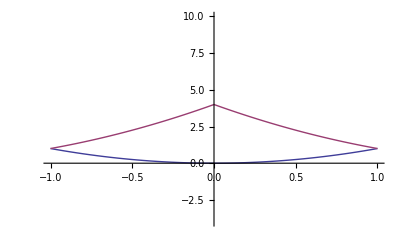

```mathematica
Plot[{eigenval[5,q,0.,0],eigenval[5,q,0.,1]},{q,-1,1},PlotRange->{-4,10}]
```

#### Plot the wannier function for a 3 Er lattice centered on a lattice site at X=0

1.40894

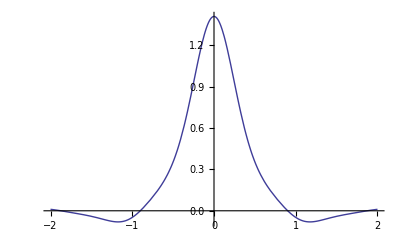

```mathematica
fun=Re[wannierfun1d[3.]]/.{X->0};
fun/.{x->0}
Plot[fun,{x,-2,2},PlotRange->All]
```

### Orthonormality relations are shown below

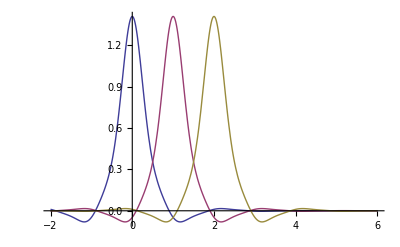

8.65901×10^-13-1.1061×10^-17 ⅈ

-1.45026×10^-12+5.84521×10^-17 ⅈ

1.-9.63427×10^-29 ⅈ

1.-1.59341×10^-28 ⅈ

```mathematica
Off[NIntegrate::ncvb]
fun1=wannierfun1d[5,3.,1]/.{X->0};
fun2=wannierfun1d[5,3.,1]/.{X->1};
fun3=wannierfun1d[5,3.,1]/.{X->2};
Plot[{Re[fun1],Re[fun2],Re[fun3]},{x,-2,6},PlotRange->All]
NIntegrate[ Conjugate[fun1] fun2,{x,-10,10}]
NIntegrate[ Conjugate[fun1] fun3,{x,-10,10}]
NIntegrate[ Conjugate[fun1] fun1,{x,-10,10}]
NIntegrate[ Conjugate[fun2] fun2,{x,-10,10}]
```

### Examples of wannier function derivatives:

#### First derivative:

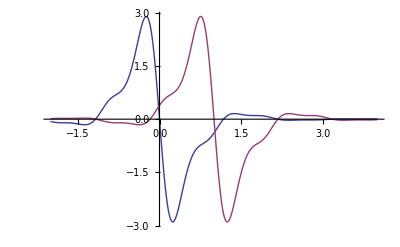

```mathematica
fun1=wannierfun1dDER[3.,1]/.{X->0};
fun2=wannierfun1dDER[3.,1]/.{X->1};
Plot[{Re[fun1],Re[fun2]},{x,-2,4},PlotRange->All]
```

#### Second derivative:

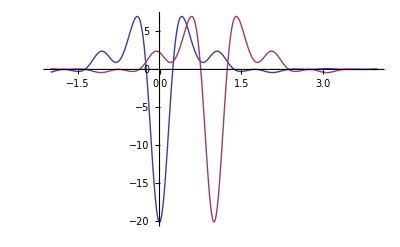

```mathematica
fun1=wannierfun1dDER[3.,2]/.{X->0};
fun2=wannierfun1dDER[3.,2]/.{X->1};
Plot[{Re[fun1],Re[fun2]},{x,-2,4},PlotRange->All]
```

## Examples of calculation of tunneling coefficients and on-site interactions

#### Make a table with some values of the tunneling coefficient and compare it to the Mathieu approximation, which is valid for deep lattices It takes about 12 seconds per point on this table.

```mathematica
Timing[tTable=Table[{v0,Re[tCalc[v0]]},{v0,1.,30.,5.}]]
```

{34.956,{{1.,0.178118},{6.,0.050773},{11.,0.0152847},{16.,0.00533392},{21.,0.0020785},{26.,0.000879326}}}

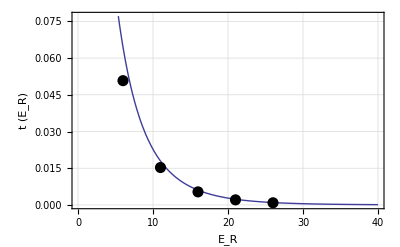

```mathematica
tMathieu[v0_]:=4/(√π)v0^(3/4)Exp[-2 √v0];
Plot[tMathieu[v0],{v0,2,40},
PlotRange->Automatic,
GridLines->Automatic,
Frame->True,FrameLabel->{"E_R","t (E_R)"},
LabelStyle->Directive[FontFamily->"Times",FontSize->22,Bold],
ImageSize->{400},
Epilog->{PointSize[0.02],Map[Point,tTable]}
]
```

## Examples of using the intepolated tunneling rate and wannier factor

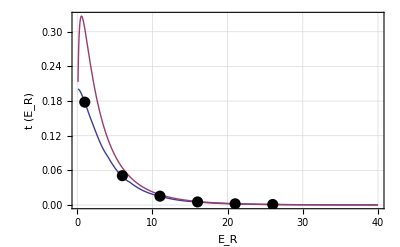

```mathematica
tMathieu[v0_]:=4/(√π)v0^(3/4)Exp[-2 √v0];
Plot[{Re[t[v0]],tMathieu[v0]},{v0,0.1,40},
PlotRange->All,
GridLines->Automatic,
Frame->True,FrameLabel->{"E_R","t (E_R)"},
LabelStyle->Directive[FontFamily->"Times",FontSize->22,Bold],
ImageSize->{400},
Epilog->{PointSize[0.02],Map[Point,tTable]}
]
```

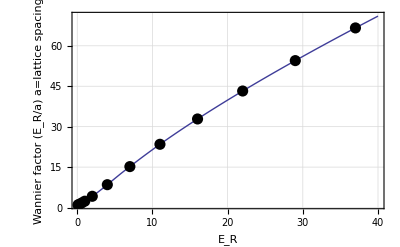

```mathematica
Plot[{wFactor[v0]},{v0,0.1,40},
PlotRange->All,
GridLines->Automatic,
Frame->True,FrameLabel->{"E_R"," Wannier factor\n (E_R/a)\n a=lattice spacing"},
LabelStyle->Directive[FontFamily->"Times",FontSize->22,Bold],
ImageSize->{400},
Epilog->{PointSize[0.02],Map[Point,wFactorTable]}
]
```

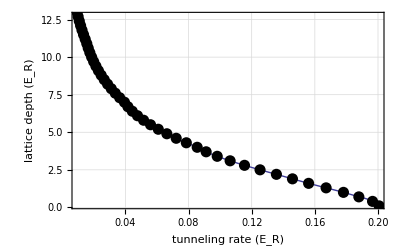

```mathematica
Plot[{v0t[t]},{t,0.2,0.01},
PlotRange->All,
GridLines->Automatic,
Frame->True,FrameLabel->{"tunneling rate (E_R)","lattice depth (E_R)"},
LabelStyle->Directive[FontFamily->"Times",FontSize->22,Bold],
ImageSize->{400},
Epilog->{PointSize[0.02],Map[Point,tInvTable]}
]
```

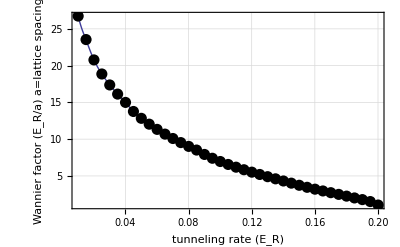

```mathematica
Plot[{wFt[t]},{t,0.2,0.01},
PlotRange->All,
GridLines->Automatic,
Frame->True,FrameLabel->{"tunneling rate (E_R)"," Wannier factor\n (E_R/a)\n a=lattice spacing"},
LabelStyle->Directive[FontFamily->"Times",FontSize->22,Bold],
ImageSize->{400},
Epilog->{PointSize[0.02],Map[Point,wFtTable]}
]
```

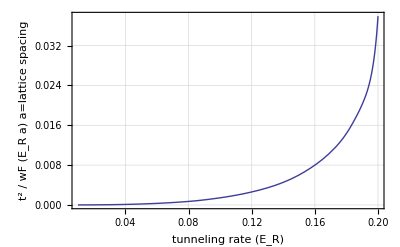

```mathematica
Plot[{t^2/wFt[t]},{t,0.2,0.01},
PlotRange->All,
GridLines->Automatic,
Frame->True,FrameLabel->{"tunneling rate (E_R)"," t^2 / wF \n (E_R a)\n a=lattice spacing"},
LabelStyle->Directive[FontFamily->"Times",FontSize->22,Bold],
ImageSize->{400}
]
```

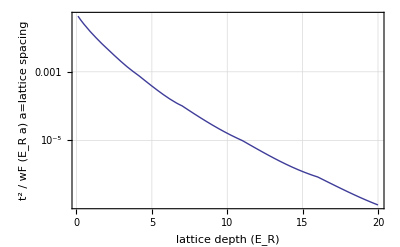

```mathematica
LogPlot[{t[v0]^2/wFactor[v0]},{v0,0.1,20.},
PlotRange->All,
GridLines->Automatic,
Frame->True,FrameLabel->{"lattice depth (E_R)"," t^2 / wF \n (E_R a)\n a=lattice spacing"},
LabelStyle->Directive[FontFamily->"Times",FontSize->22,Bold],
ImageSize->{400}
]
```

## Saving interpolation data file

### The interpolation functions for t and U are saved to a dat file, so that they can be used in the display physics program

```mathematica
Module[{head,stream,dat},
dat=Table[{v0, t[v0],wFactor[v0]},{v0,0.,56.,0.1}];
SetDirectory[NotebookDirectory[]];
head="#v0\tt(Er)\tuWannierFactor(Er/latticeSpacing)\n";
stream=OpenWrite["tANDU.dat"];
WriteString[stream,head<>ExportString[dat,"Table"]];
Close[stream];]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.